# Expressions for tip-orbital tilting

In this notebook I tried to find (and test) expressions for tip (PP) - orbital tilting with tilting of the PP.
The best matching formulas are implemented in the PP-STM code.

```mathematica
r[x_,z_]:=Sqrt[x^2+z^2]
R[x_,z_]:=Exp[-r[x,z]]
Yx[x_,z_]:=x/r[x,z]
Yz[x_,z_]:=z/r[x,z]
px[x_,z_]:=Yx[x,z]*R[x,z]
pz[x_,z_]:=Yz[x,z]*R[x,z]
```

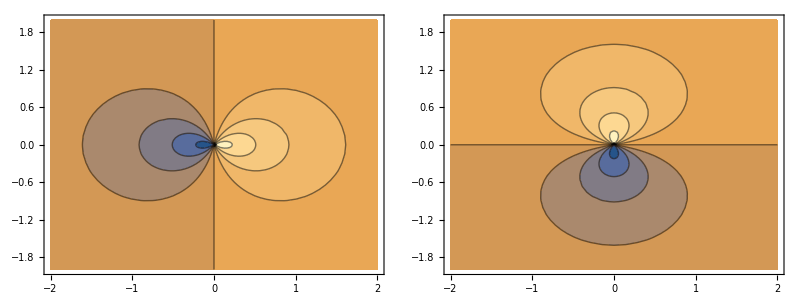

```mathematica
TableForm[{{ContourPlot[px[x,z],{x,-2,2},{z,-2,2}],ContourPlot[pz[x,z],{x,-2,2},{z,-2,2}]}}]
```

```mathematica
ArcSin[1/4]/Degree//N
```

14.4775

```mathematica
xi[a_]:=4*Sin[a*Degree];
zi[a_]:=4*(1-Cos[a*Degree]);
pix[x_,z_,xi_,zi_]:=(4+zi)/4*px[x,z]+xi/4*pz[x,z]
pi2x[x_,z_,xi_,zi_]:=(2*4-Sqrt[4^2-xi^2])/4*px[x,z]+xi/4*pz[x,z]
```

```mathematica
Manipulate[{xi[a],zi[a]},{{a,0},-15,15}]
```

```mathematica
Manipulate[{Show[ContourPlot[pix[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]],Show[ContourPlot[pi2x[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
pi3x[x_,z_,xi_,zi_]:=(4-xi)/4*px[x,z]+xi/4*pz[x,z]
```

```mathematica
Manipulate[{Show[ContourPlot[pix[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]],Show[ContourPlot[pi3x[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
piz[x_,z_,xi_,zi_]:=(4+zi)/4*pz[x,z]-xi/4*px[x,z]
```

```mathematica
Manipulate[Show[ContourPlot[piz[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2}],Plot[Sin[a*Degree]*x,{x,-2,2}]],{{a,0},-15,15}]
```

```mathematica
pialx[x_,z_,xi_,zi_,al_]:=(2*4-Sqrt[4^2-(al xi)^2])/4*px[x,z]+al xi/4*pz[x,z]
pialz[x_,z_,xi_,zi_,al_]:=(4+al*zi)/4*pz[x,z]-al xi/4*px[x,z]
```

```mathematica
Manipulate[{Show[ContourPlot[pialx[x,z,xi[a],zi[a],1],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[al*a*Degree]*x},{x,-2,2}]],Show[ContourPlot[pialz[x,z,xi[a],zi[a],1],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[al*a*Degree]*x},{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
Manipulate[{Show[ContourPlot[pialx[x,z,xi[a],zi[a],0.5],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[0.5a*Degree]*x},{x,-2,2}]],Show[ContourPlot[pialz[x,z,xi[a],zi[a],0.5],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[0.5*a*Degree]*x},{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
Manipulate[{Show[ContourPlot[pialx[x,z,xi[a],zi[a],2],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[2*a*Degree]*x},{x,-2,2}]],Show[ContourPlot[pialz[x,z,xi[a],zi[a],2],{x,-2,2},{z,-2,2},ImageSize->500],Plot[{Sin[a*Degree]*x,Sin[2*a*Degree]*x},{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
Yxz[x_,z_]:=0.5*Sqrt[15/Pi]x z/r[x,z]^2
Yx2z2[x_,z_]:=0.25*Sqrt[5/Pi](2z^2-x^2)/r[x,z]^2
Yz2[x_,z_]:=0.25*Sqrt[15/Pi](x^2-z^2)/r[x,z]^2
dxz[x_,z_]:=Yxz[x,z]*R[x,z]
dx2z2[x_,z_]:=Yx2z2[x,z]*R[x,z]
dz2[x_,z_]:=Yz2[x,z]*R[x,z]
```

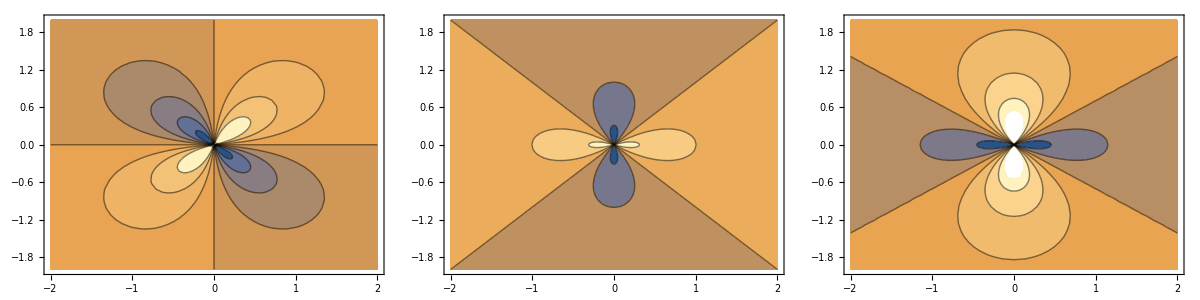

```mathematica
TableForm[{{ContourPlot[dxz[x,z],{x,-2,2},{z,-2,2}],ContourPlot[dz2[x,z],{x,-2,2},{z,-2,2}],ContourPlot[dx2z2[x,z],{x,-2,2},{z,-2,2}]}}]
```

```mathematica
di0xz[x_,z_,xi_,zi_]:=(2*4-Sqrt[4^2-(2xi)^2])/4*dxz[x,z]+(2xi)/4*dx2z2[x,z]
dix[x_,z_,xi_,zi_]:=(2*4-Sqrt[4^2-(2xi)^2])/4*dxz[x,z]-(2xi)/4*dz2[x,z]
```

```mathematica
Manipulate[{Show[ContourPlot[dxz[x*Cos[a*Degree]+z*Sin[a*Degree],z*Cos[a*Degree]-x*Sin[a*Degree]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]],Show[ContourPlot[dix[x,z,xi[a],zi[a]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]]},{{a,0},-15,15}]
```

```mathematica
dialz[x_,z_,xi_,zi_,al_]:=(4+al*2*zi)/4*dz2[x,z]+2*al* xi/4*dxz[x,z]
```

```mathematica
Manipulate[{Show[ContourPlot[dz2[x*Cos[0.55`7a*Degree]+z*Sin[a*Degree],z*Cos[a*Degree]-x*Sin[a*Degree]],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]],Show[ContourPlot[dialz[x,z,xi[a],zi[a],1],{x,-2,2},{z,-2,2},ImageSize->500],Plot[Sin[a*Degree]*x,{x,-2,2}]]},{{a,0},-15,15}]
```